# Wide-angle four-loop graphs without a Crown minor

## Complete HRF search record and cap-independent audit — 23 July 2026

Question. These 16 massless four-loop 2->2 graphs have mixed-sign derivatives but no three-loop Crown contraction minor. The original conjecture was that they have no hidden regions. This single notebook records the initial interior and low-codimension HRF searches, their closest near miss, and the later cap-independent proof for every contraction stratum from codimension four to the last nontrivial codimension.

## 1. Result

No hidden region is found in any audited stratum, and no solve is left unresolved. The conclusion does not depend on a maximum length for derivative factors, on finding a particular cancellation generator, or on assuming the special Crown presentation of F_SL.

quantity | value
graphs | 16
codimensions | 4 through E-2 for every graph
contraction strata | 108736
hidden-region strata | 0
unresolved faces | 0
complete | True

The decisive criterion is the absence of any exposed F0 face that simultaneously (i) has a positive Landau pinch and (ii) admits the required oriented hierarchy against the rest of F0, U and the restored on-shell layers.

ID | E | codimensions | strata | subtraction-free strata | face-lattice strata | sign-derivative faces | Farkas faces | HR | unresolved
85774 | 12 | {4,5,6,7,8,9,10} | 3784 | 1279 | 281 | 18515 | 32 | 0 | 0
85775 | 12 | {4,5,6,7,8,9,10} | 3784 | 1279 | 281 | 18515 | 32 | 0 | 0
85776 | 12 | {4,5,6,7,8,9,10} | 3784 | 1279 | 281 | 18515 | 32 | 0 | 0
85777 | 12 | {4,5,6,7,8,9,10} | 3784 | 1279 | 281 | 18515 | 32 | 0 | 0
105230 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0
105231 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0
105232 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 2866 | 1069 | 398799 | 274 | 0 | 0
105233 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0
105234 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0
105235 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 2866 | 1069 | 398799 | 274 | 0 | 0
105236 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 2866 | 1069 | 398799 | 274 | 0 | 0
105237 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0
105238 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0
105239 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 2866 | 1069 | 398799 | 274 | 0 | 0
105240 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0
105241 | 13 | {4,5,6,7,8,9,10,11} | 7800 | 3030 | 905 | 346561 | 306 | 0 | 0

## 2. Initial HRF search: interior through codimension three

The investigation began with the ordinary HRF obstruction search. The table records its scope exactly. The interiors, codimension one and codimension three were scanned completely. At codimension two, the stored result is the selected x8 descendant near-miss sector; it is not an all-face codimension-two enumeration.

scope | objects | exact near-miss trials | positive hierarchy gap | HR | unresolved
16 interiors | 16 | 0 | 0 | 0 | 0
codimension 1 | 204 | 20 | 0 | 0 | 0
selected codimension-2 x8 sector | 188 | 40 | 0 | 0 | 0
all codimension 3 | 4312 | 20 | 0 | 0 | 0

The only permissive codimension-three orbit is {x3,x5,x8}=0 in the twelve thirteen-propagator graphs. It produces 20 exact obstruction presentations, but every one has maximal hierarchy gap zero rather than the required strictly positive W_HR-W_SL. Diagram 105233 is a representative. Red edges in the drawing are contracted; each xi labels its Schwinger parameter.

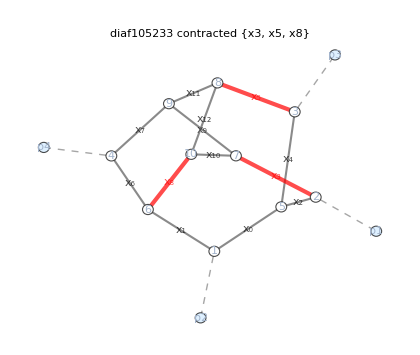

All twelve thirteen-propagator graphs have the same ordered internal topology and differ only by external-leg assignments. Contracting x3, x5 and x8 merges {2,7}, {3,8} and {6,10}. With attachment vertices a,b,c,d and core vertices e,f,g as labelled below, every one of the twelve contractions is the same unlabeled graph K4,3 with precisely the two edges a-f and d-e absent.

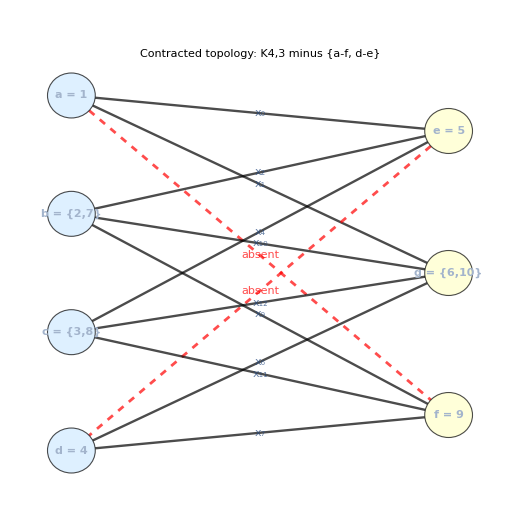

The contracted graph has E=10, V=7 and hence four loops. Vertices b and c are four-valent after their external legs are included, while g is internally four-valent. Its automorphisms exchange a<->d and b<->c independently. With p1,p2,p3,p4 fixed this gives the six pairs below; allowing crossing, all twelve graphs form one topology class.

fixed-external-label isomorphism class | exact trials per graph
{105230,105241} | 1
{105231,105238} | 3
{105232,105235} | 1
{105233,105240} | 3
{105234,105237} | 1
{105236,105239} | 1

This makes the Crown resemblance precise. The three-loop Crown is K4,2. The present graph is a maximal Crown-defective bipartite completion: neither pair among e,f,g connects to all four attachment vertices, but adding either missing edge immediately creates a literal K4,2 Crown subgraph. Adding one edge gives E=11, V=7, hence five loops; completing K4,3 gives E=12, V=7, hence six loops and contains all three possible K4,2 subgraphs. Therefore complete K4,3 is not a new five-loop seed. The natural five-loop completion already contains the known Crown seed, although it could still support additional regions beyond the inherited one.

quantity | representative value
diagram | 105233
contracted parameters | {x3,x5,x8}
generator g | (x0 x12-x1 x4) (x10 x7-x6 x9)
factorized F_SL | -((s12+s23) (x0 x12-x1 x4) (x11+x2+x4+x9) (x10 x7-x6 x9))
valid obstruction | True
strict hierarchy feasible | False
maximal gap W_HR-W_SL | 0
rho variable order | {x0,x1,x10,x11,x12,x2,x4,x6,x7,x9}
limiting oriented vector (rho;1) | {0,0,0,0,0,0,0,0,0,0,1}
active post-face sources | <|FObs→30,U→105|>

The factorized expression makes the near miss transparent: a genuine cancellation generator and a valid F_SL obstruction decomposition exist. The hierarchy inequalities nevertheless close only at gap zero. The displayed oriented vector includes the final expansion-parameter entry explicitly: (rho;1)=(0,...,0;1). Since no strictly positive W_HR-W_SL is possible, this is not a hidden region.

### All three exact generator presentations

trial | generators | generator polynomials | obstruction | strict scaling
1 | 2 | {(x0 x12-x1 x4) (x10 x7-x6 x9),(x0 x10-x1 x2) (x11 x6-x12 x7)} | True | False
2 | 1 | {(x0 x12-x1 x4) (x10 x7-x6 x9)} | True | False
3 | 1 | {(x0 x10-x1 x2) (x11 x6-x12 x7)} | True | False

All three presentations have a valid obstruction and fail the strict scaling test. Across the twelve graphs there are 20 such trials and no unresolved solve.

## 3. Kinematics and polynomial definitions

All four external momenta are algebraically incoming. In the physical wide-angle 2->2 region, s12>0, s23<0 and s13=-s12-s23<0. We use the manifestly positive coordinates a=-s23>0 and b=s12+s23=-s13>0, hence s23=-a and s12=a+b. Every Schwinger parameter xi is positive in the interior.

For each ordered graph, U is the first Symanzik polynomial and F(delta) is the second Symanzik polynomial with all external virtualities restored by the on-shell expansion parameter delta. F0 is the delta-leading coefficient. Setting xi=0 contracts the corresponding ordered internal edge. The graph definitions below therefore fix both the topology and every polynomial variable.

ID | E | ordered internal edges (x0,x1,...) | external attachments
85774 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,1},{p2,2},{p3,3},{p4,9}}
85775 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,1},{p2,2},{p3,9},{p4,3}}
85776 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,1},{p2,9},{p3,2},{p4,3}}
85777 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,9},{p2,1},{p3,2},{p4,3}}
105230 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,1},{p2,2},{p3,3},{p4,4}}
105231 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,1},{p2,2},{p3,4},{p4,3}}
105232 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,1},{p2,4},{p3,2},{p4,3}}
105233 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,1},{p3,3},{p4,4}}
105234 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,1},{p3,4},{p4,3}}
105235 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,4},{p2,1},{p3,2},{p4,3}}
105236 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,3},{p3,1},{p4,4}}
105237 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,4},{p3,1},{p4,3}}
105238 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,4},{p2,2},{p3,1},{p4,3}}
105239 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,3},{p3,4},{p4,1}}
105240 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,4},{p3,3},{p4,1}}
105241 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,4},{p2,2},{p3,3},{p4,1}}

```mathematica
SetDirectory[NotebookDirectory[]];<<"HRF_WideAngle16NoCrownAudit.wl";rawRecords=hrfWA16ParseDiagramRecords[hrfWA16InputFile[]];records=hrfWA16BuildData/@rawRecords;
```

## 4. Cap-independent higher-codimension face/pinch test

Write F0=F_SL+F_obs. Equations (13), (14) and (17) of arXiv:2607.15126 imply three exact requirements. First, all x-derivatives of F_SL vanish at one point with xi,a,b>0. Second, its monomials have one weight under rho. Third, every monomial of F_obs, U and every restored delta layer has strictly larger total weight. The second and third statements mean that the x-exponent support of F_SL is an exposed face of the F0 Newton polytope whose oriented normal extends to the augmented hierarchy.

The algorithm enumerates the complete F0 face lattice using exact rational cddlib incidences. A face is rejected if one derivative has one sign. If that fails, an exact linear (Farkas) search asks whether a constant combination of the logarithmic derivatives xi d_i F_SL is a nonzero subtraction-free polynomial. Such a polynomial is strictly positive in the physical orthant but would vanish at a common pinch. Only the remaining faces require an exact normalized FindInstance solve. Any positive pinch is finally passed to the oriented (rho;1) hierarchy LP.

```mathematica
<<"HRF_WideAngle16FacePinchAudit.wl";hrfWA16FacePinchAudit[records⟦1⟧,{x0,x3,x5,x6}]
```

## 5. Positive control: the three-loop Crown

The same presentation-independent algorithm must retain the known Crown hidden region. It finds exactly one positive pinch face. The witness has all xi=1 and a=b=1; the hierarchy LP gives rho_i=-1, W_SL=-4 and gap 1.

F0 faces | 27
positive pinch-and-hierarchy faces | 1
F_SL | s12 x1 x3 x4 x6-s12 x1 x2 x5 x6-s23 x1 x2 x5 x6+s23 x0 x3 x5 x6+s23 x1 x2 x4 x7-s12 x0 x3 x4 x7-s23 x0 x3 x4 x7+s12 x0 x2 x5 x7
pinch witness | {x0→1,hrfWA16A→1,hrfWA16B→1,x1→1,x2→1,x3→1,x4→1,x5→1,x6→1,x7→1}
scaling | {x0→-1,x1→-1,x2→-1,x3→-1,x4→-1,x5→-1,x6→-1,x7→-1}
W_SL | -4
gap | 1

## 6. Representative higher-codimension Farkas near miss

Diagram 85774 on the contraction {x0,x3,x5,x6}=0 contains faces for which no single derivative is sign-definite. The stronger log-derivative certificate closes them. The displayed rational coefficients c_i produce P=sum_i c_i xi d_i F_SL with nonnegative coefficients and P not identically zero. Thus P>0 for xi,a,b>0, contradicting a simultaneous pinch.

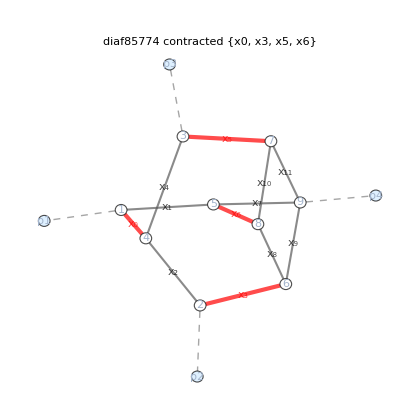

### Exact face and Farkas certificate

#### F_SL

-s12 x1 x10 x11 x2 x7-s23 x1 x10 x11 x2 x7-s12 x1 x10 x11 x2 x8-s23 x1 x10 x11 x2 x8-s12 x1 x11 x2 x7 x8-s23 x1 x11 x2 x7 x8-s12 x10 x11 x2 x7 x8-s23 x10 x11 x2 x7 x8-s12 x11 x2 x4 x7 x8-s23 x11 x2 x4 x7 x8-s12 x1 x10 x11 x2 x9-s23 x1 x10 x11 x2 x9+s12 x1 x10 x4 x7 x9+s12 x10 x2 x4 x7 x9+s12 x1 x10 x4 x8 x9+s12 x1 x11 x4 x8 x9+s12 x1 x4 x7 x8 x9+s12 x10 x4 x7 x8 x9

#### Combination coefficients

{1/50,1/50,1/50,-2/25,1/50,1/50,1/50,1/50}

#### Strictly positive combination polynomial

1/10 hrfWA16A x1 x10 x4 x7 x9+1/10 hrfWA16B x1 x10 x4 x7 x9+1/10 hrfWA16A x1 x10 x4 x8 x9+1/10 hrfWA16B x1 x10 x4 x8 x9+1/10 hrfWA16A x1 x11 x4 x8 x9+1/10 hrfWA16B x1 x11 x4 x8 x9+1/10 hrfWA16A x1 x4 x7 x8 x9+1/10 hrfWA16B x1 x4 x7 x8 x9+1/10 hrfWA16A x10 x4 x7 x8 x9+1/10 hrfWA16B x10 x4 x7 x8 x9

A larger thirteen-propagator mixed-sign example, diagram 105232 with {x0,x1,x3,x5}=0, has 1,207 F0 faces. Every face is rejected algebraically and no nonlinear ambiguity remains.

<|ID→105232,ZeroVars→{x0,x1,x3,x5},F0PointCount→14,F0FacetCount→15,FaceCount→1207,FaceStatusCounts→<|RejectedBySignDefiniteDerivative→1207|>,UnresolvedFaceCount→0|>

## 7. Why long derivative factors cannot reopen the result

The historical eight-monomial cutoff has been removed from HRF: $HRFPolynomialMaxDerivativeMonomials is now fixed to Infinity, and the current raw harvest resets its per-polynomial state on every stratum. The uncapped factor prefilter consequently retains many more candidate presentations. None of those presentations can evade the face/pinch proof, because any HR—whatever generators or polynomial multipliers describe it—must select one of the enumerated F0 faces and satisfy the same pinch and hierarchy equations.

The graph-theoretic observation 'no Crown contraction minor' therefore remains a useful classifier, but it is not used as the proof. The proof is the stronger polynomial statement: every possible F_SL face is subtraction-free, has a sign-definite derivative, or has a subtraction-free linear combination of logarithmic derivatives; any exceptional positive pinch would still have to pass the exact hierarchy LP.

This sharpens the earlier evidence at the bottom of p. 19 of arXiv:2407.13738, where the individual channel coefficients admitted separate solutions but no common solution was found when both wide-angle invariants were active.

## 8. Graph drawings

The labels x0,x1,... follow the ordered internal-edge lists in Section 3. External legs are dashed.

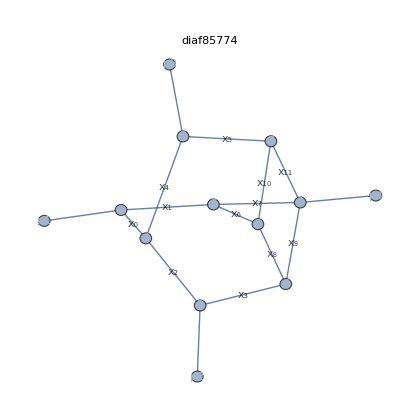
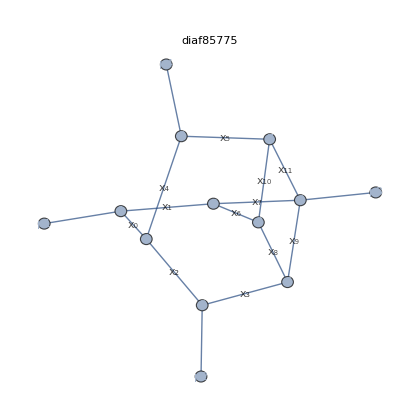
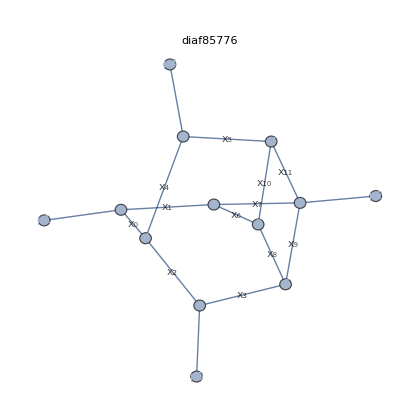
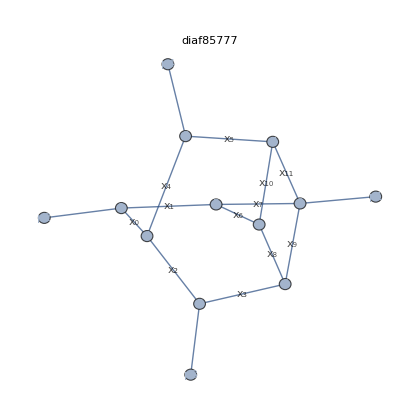
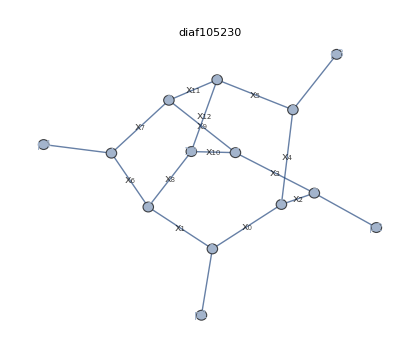
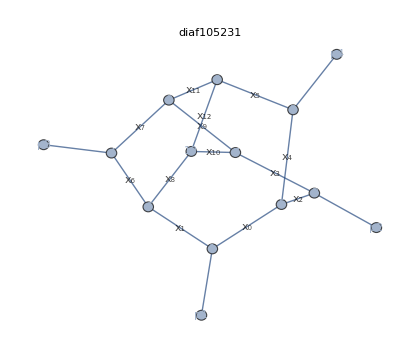
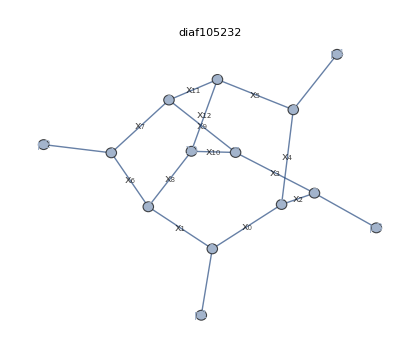
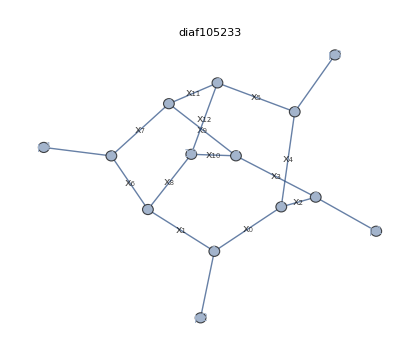

## 9. Polynomial inventory and reproducibility

ID | variables | U terms | F0 terms | highest restored delta layer
85774 | 12 | 225 | 90 | 1
85775 | 12 | 225 | 90 | 1
85776 | 12 | 225 | 90 | 1
85777 | 12 | 225 | 90 | 1
105230 | 13 | 315 | 141 | 1
105231 | 13 | 315 | 141 | 1
105232 | 13 | 315 | 141 | 1
105233 | 13 | 315 | 141 | 1
105234 | 13 | 315 | 141 | 1
105235 | 13 | 315 | 141 | 1
105236 | 13 | 315 | 141 | 1
105237 | 13 | 315 | 141 | 1
105238 | 13 | 315 | 141 | 1
105239 | 13 | 315 | 141 | 1
105240 | 13 | 315 | 141 | 1
105241 | 13 | 315 | 141 | 1

The full expressions are generated, not imported as unexplained symbols: makeFourPointOnShellF0 constructs U, F0 and F(delta) from the displayed edge lists and external attachments. The following association exposes every expression for direct inspection.

```mathematica
allPolynomials=Association[(#ID->Association["Variables"->#Vars,"U"->#U,"F0"->#F0,"F(delta)"->#Data["FOnShell"]]&)/@records]
```

```mathematica
<<"HRF_WideAngle16FacePinchRegressionTests.wl";hrfRunWA16FacePinchRegressionTests[]
```

```mathematica
RunProcess[{"wolframscript","-file","run_wa16_face_pinch_depth_batch.wl","min=4","85774"}]
```

Low-codimension inputs are results/wide_angle_16_current_audit_summary.wl, results/wide_angle_16_stored_boundaries_current_gap_summary.wl, results/wide_angle_16_codim3_hierarchy_gap_summary.wl and results/wide_angle_16_codim3_nearmiss_105233.wl. Higher-codimension primary files are HRF_WideAngle16FacePinchAudit.wl (certificate), run_wa16_face_pinch_depth_batch.wl (checkpointed exhaustive runner), aggregate_wa16_face_pinch_audit.wl (summary), and HRF_WideAngle16FacePinchRegressionTests.wl (Crown plus negative controls). cddexec is used only for exact Newton-face incidences.

## 10. References

E. Gardi et al., arXiv:2407.13738, especially the discussion at the bottom of p. 19 (original no-Crown evidence and dissection framework).

E. Gardi et al., arXiv:2607.15126, Eqs. (13)–(17) (pinch, homogeneous F_SL, ideal presentation and strict hierarchy conditions).